```mathematica
<<IGraphM`
Nn=(32)^2;(*number of spins*)mcs=100;(*Monte Carlo steps*)J=1;(*interaction strength*)
kT=Range[3.6,1,-0.2];(*range of temperatures*)NkT=Length[kT];
b=0;
this = 1;
bσ=RandomChoice[{1,-1},Nn];(*random initial state*)
```

IGAdjacencyMatrixPlot::shdw: Symbol IGAdjacencyMatrixPlot appears in multiple contexts {IGraphM`,Global`}; definitions in context IGraphM` may shadow or be shadowed by other definitions.

IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

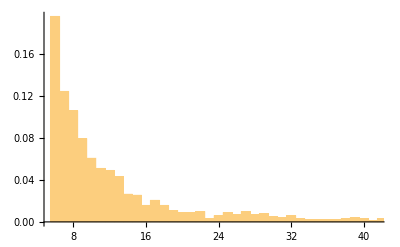

Show::gtype: Global`IGAdjacencyMatrixPlot is not a type of graphics.

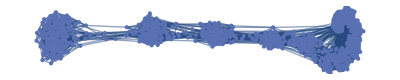
Show[Global`IGAdjacencyMatrixPlot[-Graphics-]]

```mathematica
myArewAss = Import["/home/albertoartoni/Desktop/reteRight.dat"];
myA = myArewAss;
Histogram[VertexDegree@graph,1000,"PDF"]
b=0; 
kT=Range[4,1,-0.2];(*range of temperatures*)NkT=Length[kT];
bσ=RandomChoice[{1,-1},Nn];(*random initial state*)
(* simmetry and deltaH*)
(* step iniziale per la h *)
plotAdjMatrix[myArewAss]
ArrayPlot[{1/2 (bσ+1)},Mesh->All];
```

```mathematica
plotTimeEvolution[input_]:=Module[{time = input},ArrayPlot[1/2 (Transpose[time]+1)]];
```

```mathematica
pathTmp = "/home/albertoartoni/Desktop/Discussione/Immagini/IsingAssortative/animation";
For[jj=1,jj<= 100,jj++,
vettW = Table[0,{mj,1,Nn}];
vettB = Table[0,{j,1,Nn}];
j=1;l=1;
For[k=1,k <= Nn,k++,
If[time[[jj*10]][[k]] == 1,vettW[[j]]=k; j++,vettB[[l]]=k;l++];];
testPlot=Show[HighlightGraph[graph,{vettW,vettB},VertexSize->.5]];
If[jj<10,
path=pathTmp<>ToString[0]<>ToString[jj]<>".png",path=pathTmp<>ToString[jj]<>".png"];
Export[path,testPlot];
Print["Export ",jj," succeded"];]

(* okay, visualizza da sx verso alto, prima colonna, poi seconda colonna e così via*}
```

Export 1 succeded

Export 2 succeded

Export 3 succeded

Export 4 succeded

Export 5 succeded

Export 6 succeded

Export 7 succeded

Export 8 succeded

Export 9 succeded

Export 10 succeded

Export 11 succeded

Export 12 succeded

Export 13 succeded

Export 14 succeded

Export 15 succeded

Export 16 succeded

Export 17 succeded

Export 18 succeded

Export 19 succeded

Export 20 succeded

Export 21 succeded

Export 22 succeded

Export 23 succeded

Export 24 succeded

Export 25 succeded

Export 26 succeded

Export 27 succeded

Export 28 succeded

Export 29 succeded

Export 30 succeded

Export 31 succeded

Export 32 succeded

Export 33 succeded

Export 34 succeded

Export 35 succeded

Export 36 succeded

Export 37 succeded

Export 38 succeded

Export 39 succeded

Export 40 succeded

Export 41 succeded

Export 42 succeded

Export 43 succeded

Export 44 succeded

Export 45 succeded

Export 46 succeded

Export 47 succeded

Export 48 succeded

Export 49 succeded

Export 50 succeded

Export 51 succeded

Export 52 succeded

Export 53 succeded

Export 54 succeded

Export 55 succeded

Export 56 succeded

Export 57 succeded

Export 58 succeded

Export 59 succeded

Export 60 succeded

Export 61 succeded

Export 62 succeded

Export 63 succeded

Export 64 succeded

Export 65 succeded

Export 66 succeded

Export 67 succeded

Export 68 succeded

Export 69 succeded

Export 70 succeded

Export 71 succeded

Export 72 succeded

Export 73 succeded

Export 74 succeded

Export 75 succeded

Export 76 succeded

Export 77 succeded

Export 78 succeded

Export 79 succeded

Export 80 succeded

Export 81 succeded

Export 82 succeded

Export 83 succeded

Export 84 succeded

Export 85 succeded

Export 86 succeded

Export 87 succeded

Export 88 succeded

Export 89 succeded

Export 90 succeded

Export 91 succeded

Export 92 succeded

Export 93 succeded

Export 94 succeded

Export 95 succeded

Export 96 succeded

Export 97 succeded

Export 98 succeded

Export 99 succeded

Export 100 succeded

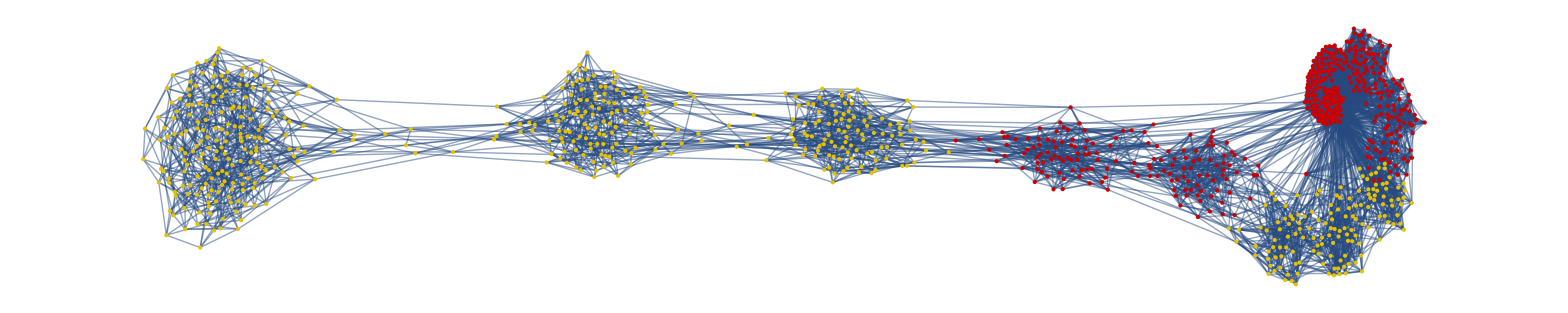

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
vettW = Table[0,{mj,1,Nn}];
vettB = Table[0,{j,1,Nn}];
item = Nn;
elems = Table[i,{i,1,item}];
graph = AdjacencyGraph[adjancySorted[[elems,elems]]];
j=1;l=1;
For[k=1,k <= item,k++,
If[time[[1000]][[k]] == 1,vettW[[j]]=k; j++,vettB[[l]]=k;l++];];
HighlightGraph[graph,{vettW,vettB}, VertexSize->1, EdgeStyle->Thick]
```

```mathematica
MetropolisMajority[input_,inputA_,mcs2_] := Module[{bσ = input,myA=inputA,mcs=mcs2},
time = Table[Table[0,{jj,1,Nn}],{j,1,mcs+1}];
time[[1]]=Table[bσ[[jj]],{jj,1,Nn}];
Timing[
iT = NkT;
(*β=1/kT*)
For[kk=2,kk≤mcs+1,kk++,
(*Monitor[*)
For[t=1,t≤Nn,t++,
(*loop over Monte Carlo steps*)(*choose the spin to flip*)
xflip=RandomInteger[{1,Nn}];
h=0;
vIdx = AdjacencyList[gMetro,xflip,1];dimIdx = Length[vIdx];
h = h - 2*b*bσ[[xflip]];
For[j=1, j <= dimIdx,j++,
	h = -2*J*bσ[[vIdx[[j]]]]*(-bσ[[xflip]])*myA[[xflip]][[vIdx[[j]]]] + h;];
If[h≠0,
α=Min[1,1/(1+Exp[2*β h])],α=0.5;];
(*α = Min[1,Exp[-β h]];*)
u=RandomReal[{0,1}];
If[u≤α,
bσ[[xflip]]=-bσ[[xflip]],bσ[[xflip]]= bσ[[xflip]];];
(* prova ad usare adjacency list*)
(*
For[j=1, j <= dimIdx,j++,
h = myA[[xflip]][[vIdx[[j]]]]*bσ[[vIdx[[j]]]]+h];
If[ h>0, bσ[[xflip]]=1; ];
If[h<0,bσ[[xflip]]=-1; ];
(*If[h==0,bσ[[xflip]]=-bσ[[xflip]]];*)
If[h==0,α = RandomReal[{0,1}];If[α≤ 0.5, bσ[[xflip]] = -bσ[[xflip]],bσ[[xflip]] = bσ[[xflip]]]; ]; *)
];
time[[kk]]=Table[bσ[[jj]],{jj,1,Nn}];
(*If[Mod[kk,mcs/10]==0,Print["Current mcs: ",kk]]*)
];
ArrayPlot[{1/2 (bσ+1)},Mesh->All]]];
```

```mathematica
bσ=RandomChoice[{1,-1},Nn];
```

```mathematica
gMetro = AdjacencyGraph[adjancySorted];
tempSize = 400;
mcs = 1000;
results = Table[0,{i,1,tempSize}];
myT = Table[i/20,{i,1,tempSize}];
time = Table[Table[0,{jj,1,Nn}],{j,1,mcs+1}];
time[[mcs]] = bσ;
For[jj=1,jj<=tempSize,jj++,
β=1/myT[[jj]];
MetropolisMajority[time[[mcs]],adjancySorted,mcs];
results[[jj]] = time[[mcs]];
If[Mod[jj,tempSize/20]==0,Print["Current ride: ",jj]];
]
(*ArrayPlot[1/2 (Transpose[time]+1),Mesh->{lines,{1}},ImageSize->500]*)
```

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1-1/(1+1/ⅇ^320).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1-1/(1+1/ⅇ^160).

General::stop: Further output of Min::meprec will be suppressed during this calculation.

Current ride: 20

Current ride: 40

Current ride: 60

Current ride: 80

Current ride: 100

Current ride: 120

Current ride: 140

Current ride: 160

Current ride: 180

Current ride: 200

Current ride: 220

Current ride: 240

Current ride: 260

Current ride: 280

Current ride: 300

Current ride: 320

Current ride: 340

Current ride: 360

Current ride: 380

Current ride: 400

```mathematica
l
graph = AdjacencyGraph[adjancySorted];
graphDegrees = VertexDegree@graph;
mapDegreeNode = Table[{graphDegrees[[i]],i},{i,1,1024}];
mapDegreeNodeSorted = Sort[mapDegreeNode];
timeS = Table[Table[0,{j,1,Dimensions[time][[2]]}],{k,1,Dimensions[time][[1]]}];
For[kk=1,kk≤Dimensions[time][[1]],kk++,
For[jj=1,jj≤Dimensions[time][[2]],jj++,
timeS[[kk]][[mapDegreeNodeSorted[[jj]][[2]]]]=time[[kk]][[jj]];]]
```

366

```mathematica
xflip =vIdx[[3]]
timeS[[1000]][[xflip]]
vIdx = AdjacencyList[gMetro,xflip,1]
bσ[[vIdx]]=1
```

```mathematica
β
```

1/20

```mathematica
h
ArrayPlot[Transpose[results],Mesh->{lines,{1}},ColorRules->{1->Black,-1->White},ImageSize->500,Axes->True,AxesLabel->{"T","bσ"}]
```

8

-Graphics-

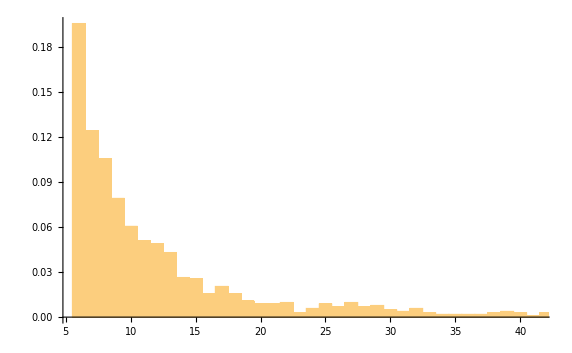

```mathematica
lines;
For[ jj=lines[[3]],jj≤Nn,jj++,
For[kk= 1,kk≤ lines[[1]],kk++,
adjancySorted[[jj,kk]] = 0;
adjancySorted[[kk,jj]] = 0;]]
adjancySorted // MatrixPlot;
Histogram[VertexDegree[graph],1000,"PDF"]
```

```mathematica
plotAdjMatrix[myAStar_]:=Module[{myA=myAStar},
graph = AdjacencyGraph[myA];
graphDegrees = VertexDegree@graph;
mapDegreeNode = Table[{graphDegrees[[i]],i},{i,1,Nn}];
mapDegreeNode = Sort[mapDegreeNode];
adjancySorted = Table[Table[0,{jjj,1,Nn}],{kkk,1,Nn}];
For[k=1,k<=Nn,k++,
For[l=1,l<k,l++,
If[myA[[ mapDegreeNode[[k]][[2]] ]][[mapDegreeNode[[l]][[2]]]] ==1,
adjancySorted[[k]][[l]] = 1;
adjancySorted[[l]][[k]] = 1;
];]];
IGAdjacencyMatrixPlot[graph];
graph2 = AdjacencyGraph[adjancySorted];
Show[IGAdjacencyMatrixPlot[graph2]]]
```

```mathematica
(*Export["/home/albertoartoni/Desktop/Discussione/Immagini/Esempio4/reteArewAss.dat",myArewAss];
Export["/home/albertoartoni/Desktop/Discussione/Immagini/Esempio4/retemyA.dat",myA];*)

myArewAss = Import["/home/albertoartoni/Desktop/reteRight.dat"];
myA = myArewAss;
plotAdjMatrix[myArewAss]
```

Table::iterb: Iterator {i,1,Nn} does not have appropriate bounds.

Table::iterb: Iterator {kkk,1,Nn} does not have appropriate bounds.

AdjacencyGraph::matsq: Argument Table[Table[0,{jjj,1,Nn}],{kkk,1,Nn}] at position 1 is not a non-empty square matrix.

Show::gtype: IGAdjacencyMatrixPlot is not a type of graphics.

Show[IGAdjacencyMatrixPlot[AdjacencyGraph[Table[Table[0,{jjj,1,Nn}],{kkk,1,Nn}]]]]

```mathematica
MatrixPlot[adjancySorted,Mesh->{lines,lines}]
```

MatrixPlot::mat0: Argument adjancySorted at position 1 is not a matrix.

MatrixPlot[adjancySorted,Mesh→{lines,lines}]

```mathematica
Nn = 1024;
γ = 2.1;
Print["Min dis: ",-Nn^(2-γ)/(γ-1)];
γ = 2.9;
Nn^(-1/(γ^2-1))
γ = 2.5;
-Nn^(-2-γ)/(γ-1)
```

Min dis: -0.454545

0.392421

-1.89478×10^-14

```mathematica
myLines[myAinput_,maxLinesInput_]:=Module[{myA=myAinput,maxLines=maxLinesInput},
graph = AdjacencyGraph[myA];
graphDegrees = VertexDegree@graph;
levels = BinCounts[Sort[graphDegrees]];
length = Length[levels];
count = 0;
iter = 1;
lines = Table[0,{i,1,maxLinesInput}];
For[k=1,k<=length,k++,
If[levels[[k]]≠0 && iter <= maxLines,lines[[iter]]=levels[[k]]+count; iter++; count = levels[[k]]+count;]
]]
```

```mathematica
myLines[myArewAss,10]
	lines
```

{200,327,435,516,578,630,680,724,751,777}

139

```mathematica
totalRew
```

5244

```mathematica
graphDegrees = VertexDegree@graph; degSort = Sort[Table[{graphDegrees[[i]],i,Table[time[[j]][[i]],{j,1,mcs}]},{i,1,Nn}]];
vett = Table[degSort[[i]][[3]],{i,1,Nn}];
plotTimeEvolution[Transpose[vett]]
ArrayPlot[1/2 (vett+1),Mesh->{{49,85,115},{1}}]
```

```mathematica
(* okay, potrei riscrivere il rewire in funzione di edge list*)
graph = AdjacencyGraph[myA];
lista = IGIndexEdgeList[graph];
```

1

```mathematica
While[ll<100,ll++;If[(myArewAss[[ll]][[ll]] == 1), Print["Loop!"];]]
```

```mathematica
FindGraphCommunities[graph];
CommunityGraphPlot[graph]
mapDegreeNode;
```

```mathematica
test = adjancySorted;
out = Table[Table[0,{ii,1,Nn}],{jj,1,Nn}];

maskRow = Table[Boole[adjancySorted[[ii]][[1]] == 1],{ii,1,Nn}];
maskCol= Table[Boole[adjancySorted[[ii]][[1]] != 1],{ii,1,Nn}];
iter = 1;
For[k=1,k≤Nn,k++,
If[maskRow[[k]]>0,
   For[l=1,l≤Nn,l++,out[[iter]][[l]]=test[[k]][[l]];]iter++;]] 
For[k=1,k≤Nn,k++,
If[maskRow[[k]]==0,
   For[l=1,l≤Nn,l++,out[[iter]][[l]]=test[[k]][[l]];]iter++;]] 
iter = 1;
For[k=1,k≤Nn,k++,
If[maskCol[[k]]>0,
   For[l=1,l≤Nn,l++,out[[l]][[iter]]=test[[l]][[k]];]iter++;]] 
For[k=1,k≤Nn,k++,
If[maskCol[[k]]==0,
   For[l=1,l≤Nn,l++,out[[l]][[iter]]=test[[l]][[k]];]iter++;]] 
out[[Nn-2,1]]
out[[1,Nn-2]]
```

0

1

```mathematica
myA =Import["/home/albertoartoni/Desktop/Discussione/Matlab/reteArewAss.mat"][[1]];
graph = AdjacencyGraph[myA];
```

```mathematica
(* create a map 
prendo i primi nodi dal grado mass*)
graphDegrees   = VertexDegree@graph;
graphDegreesS = Sort[graphDegrees];
out = Table[0,{i,1,Nn}];
iter =Length[graphDegrees];
outIter=1;
For[iter=Nn,iter≥1,iter--,
curK = mapDegreeNode[[iter]][[2]];
For[l=1,l≤Nn,l++,
dummy=True;
For[jj=1,jj≤outIter,jj++,
If[l==out[[jj]],dummy=False;Break[]];];
If[myArewAss[[curK]][[l]] == 1 && dummy , out[[outIter]] = l; outIter++]];]
```

```mathematica
β = Infinity;
α=Min[1,1/(1+Exp[-2*β h*0])]
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
h
```

9